## 1 Initialisation

### 1.1 Import demand datasets

```mathematica
(*All datasets should be stored in a folder called "DataDir".*)
SetDirectory[FileNameJoin[{NotebookDirectory[],"DataDir"}]];
```

```mathematica
hourlydemand09to23=Import["exp_hourly_total_demand09to23.csv"];
hourlyDemandTS=TimeSeries[ToExpression[#]&/@hourlydemand09to23]
```

TemporalData[TimeSeries, «1»]

```mathematica
monthlyTotalDemand09to23=Import["exp_monthly_total_demand09to23.csv"];
monthlyTotalDemandTS=TimeSeries[ToExpression[#]&/@monthlyTotalDemand09to23]
```

TimeSeries[…]

### 1.2 Accuracy measures

#### MAPE

-Graphics-

-Graphics-

```mathematica
mape[prediction_,actual_]:=Module[
{APE,n,MAPE},
n=Length[actual];
APE=Table[Abs[100 * (actual[[i]]-prediction[[i]])/actual[[i]]],{i,1,n}];
MAPE=Mean[APE]
]
```

#### sMAPE

-Graphics-

```mathematica
smape[prediction_,actual_]:=Module[
{sAPE,n,sMAPE},
n=Length[actual];
sAPE=Table[100 *Abs[actual[[i]]-prediction[[i]]]/(Abs[actual[[i]]]+Abs[prediction[[i]]]),{i,1,n}];
sMAPE=2* Mean[sAPE]
]
```

#### MASE

-Graphics-

-Graphics-

```mathematica
mase[prediction_,actual_]:=Module[
{Q,n,MASE},
n=Length[actual];
Q=Table[(actual[[i]]-prediction[[i]]),{i,1,n}];
MASE=Mean[Abs[Q]]/Mean[Abs[Differences[actual]]]
]
```

## 2 Traditional Model

### 2.1 Tests

```mathematica
RegularlySampledQ[monthlyTotalDemandTS]
```

True

The data is auto-correlated, an auto-regressive model will be needed.

```mathematica
AutocorrelationTest[monthlyTotalDemandTS]
```

1.07554×10^-43

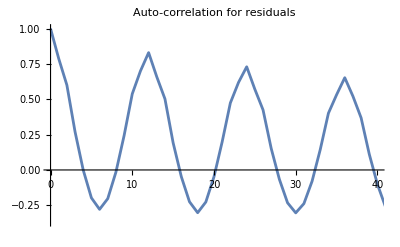

```mathematica
ListLinePlot[CorrelationFunction[monthlyTotalDemandTS,{160}],PlotLabel->"Auto-correlation for residuals",PlotRange->{{0,40},All}]
```

The data is not stationary. An integrated model of order 1 would make the time series stationary but so would a seasonal model of period 12 months. Both Integrated and Seasonal components may not be required in the model.

```mathematica
UnitRootTest[monthlyTotalDemandTS]
```

0.506865

```mathematica
UnitRootTest[Differences[monthlyTotalDemandTS]]
```

1.70712×10^-11

```mathematica
UnitRootTest[Differences[monthlyTotalDemandTS,1,12]]
```

2.23183×10^-8

From the ACF plot we see that we have a strong seasonal pattern repeating at 12 lags.
The PACF shows potentially an order 2 on the auto-regressive model at lag 1 and lag 3. The rapid decay from lag 1 to lag 2 is an indication that there is no moving average component.

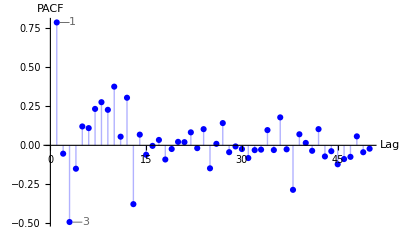

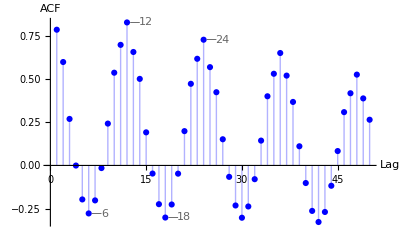

```mathematica
figC2=ListPlot[PartialCorrelationFunction[monthlyTotalDemandTS,{1,50}],Filling->Axis,PlotRange->All,AxesLabel->{"Lag","PACF"},
PlotStyle->Blue,
Epilog->{{Directive[Black,Thickness[0.001]],
Line[{{1.5,0.788},{3,0.788}}],
Line[{{3.5,-0.492},{5,-0.492}}]},
GrayLevel[0.4],
Text["1",{3.5,0.788}],
Text["3",{5.5,-0.492}]
}]
figC1=ListPlot[CorrelationFunction[monthlyTotalDemandTS,{1,50}],Filling->Axis,PlotRange->All,AxesLabel->{"Lag","ACF"},
PlotStyle->Blue,
Epilog->{{Directive[Black,Thickness[0.001]],
Line[{{12.5,0.83},{14,0.83}}],
Line[{{24.5,0.73},{26,0.73}}],
Line[{{6.5,-0.279},{8,-0.279}}],
Line[{{18.5,-0.302},{20,-0.302}}]},
GrayLevel[0.4],
Text["12",{14.9,0.83}],
Text["24",{26.9,0.73}],
Text["6",{8.5,-0.279}],
Text["18",{20.9,-0.302}]
}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","FigureC1.png"}],figC1];
Export[FileNameJoin[{NotebookDirectory[],"Figures","FigureC2.png"}],figC2];
```

### 2.2 Modelling

#### 2.2.1 On monthly data

```mathematica
trainingMonthly=TimeSeries[{DateObject[monthlyTotalDemandTS["Times"][[#]]],monthlyTotalDemandTS["Values"][[#]]}&/@Range[120]]
testingMonthly=TimeSeries[{DateObject[monthlyTotalDemandTS["Times"][[#]]],monthlyTotalDemandTS["Values"][[#]]}&/@Range[121,156]]
```

TimeSeries[…]

TimeSeries[…]

```mathematica
traditionalModelMonthly=TimeSeriesModelFit[trainingMonthly]
```

TimeSeriesModel[…]

The AIC (Akaike Information Criterion) score measures how good each candidate model is - lower values are better. AIC takes into account how likely the data could have come out of each model, and also how many parameters the model has. Models with many parameters are penalised, so that the fitting tries to find a balance between a model that agrees with the data as much as possible, but also is not too complex and does not over-fit.

```mathematica
traditionalModelMonthly["CandidateSelectionTable"]
```

| Candidate | AIC
1 | SARIMAProcess[{1,0,0},{0,1,2}_12] | 3425.87
2 | SARIMAProcess[{1,0,0},{0,1,3}_12] | 3429.1
3 | SARIMAProcess[{1,0,0},{1,1,1}_12] | 3429.51
4 | SARIMAProcess[{1,0,1},{0,1,2}_12] | 3431.19
5 | SARIMAProcess[{1,0,0},{0,1,1}_12] | 3431.96
6 | SARIMAProcess[{2,0,0},{0,1,2}_12] | 3432.62
7 | SARIMAProcess[{2,0,0},{0,1,1}_12] | 3432.94
8 | SARIMAProcess[{1,0,0},{1,1,2}_12] | 3434.31
9 | SARIMAProcess[{1,0,0},{1,1,3}_12] | 3436.3
10 | SARIMAProcess[{1,0,1},{0,1,1}_12] | 3438.6

Not all the parameters from the top model are significant.

```mathematica
traditionalModelMonthly["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 0.382017 | 0.345881 | 1.10448 | 0.135798
β_1 | -0.839147 | 0.0885299 | -9.47868 | 1.50274×10^-16
β_2 | 0.243915 | 0.0885299 | 2.75517 | 0.00339046

The residuals are uncorrelated.

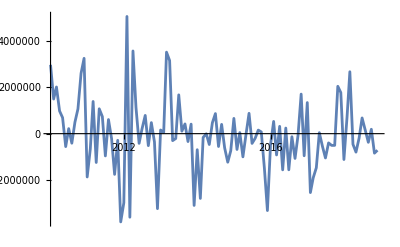

```mathematica
ListLinePlot[traditionalModelMonthly["FitResiduals"]]
```

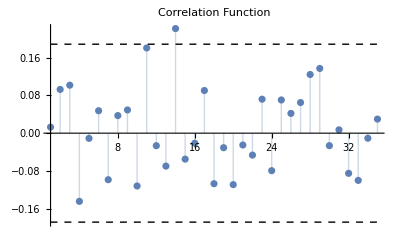

```mathematica
traditionalModelMonthly["ACFPlot"]
```

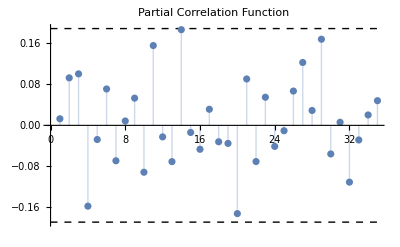

```mathematica
traditionalModelMonthly["PACFPlot"]
```

```mathematica
AutocorrelationTest[traditionalModelMonthly["FitResiduals"]]
```

0.472843

#### 2.2.2 On hourly data

```mathematica
trainingHourly=TimeSeries[{DateObject[hourlyDemandTS["Times"][[#]]],hourlyDemandTS["Values"][[#]]}&/@Range[87648]]
testingHourly=TimeSeries[{DateObject[hourlyDemandTS["Times"][[#]]],hourlyDemandTS["Values"][[#]]}&/@Range[87649,113952]]
```

TemporalData[TimeSeries, «1»]

TimeSeries[…]

```mathematica
traditionalModelHourly=TimeSeriesModelFit[trainingHourly,{"SARIMA",{{Automatic,Automatic,Automatic},{Automatic,Automatic,Automatic},12}}]
```

6                                        6                                                                                                              6
TimeSeriesModel[Automatic, {TemporalData[TimeSeries, «1»], {SARIMA, «6», {Candidates -> {SARMAProcess[826.012, {1.57815, -0.858788, 0.236937}, {}, {12, {0.0170132, 0.817276, -0.0501449}, {}}, 1.81598 10 ], SARMAProcess[820.104, «3», 1.81637 10 ], «7», SARMAProcess[913.799, {1.45023, -0.507474}, {}, {12, {-0.00722804, 0.832796}, {-0.0109787}}, 1.9147 10 ]}, AIC -> {«10»}}}, {}}]

The AIC (Akaike Information Criterion) score measures how good each candidate model is - lower values are better. AIC takes into account how likely the data could have come out of each model, and also how many parameters the model has. Models with many parameters are penalised, so that the fitting tries to find a balance between a model that agrees with the data as much as possible, but also is not too complex and does not over-fit.

```mathematica
traditionalModelHourly["CandidateSelectionTable"]
```

| Candidate | AIC
1 | SARMAProcess[{3,0},{3,0}_12] | 1.26321×10^6
2 | SARMAProcess[{3,0},{3,1}_12] | 1.26323×10^6
3 | SARMAProcess[{3,0},{2,0}_12] | 1.26358×10^6
4 | SARMAProcess[{3,0},{2,1}_12] | 1.26365×10^6
5 | SARMAProcess[{4,0},{3,0}_12] | 1.26402×10^6
6 | SARMAProcess[{4,0},{2,0}_12] | 1.26436×10^6
7 | SARMAProcess[{2,0},{3,0}_12] | 1.26712×10^6
8 | SARMAProcess[{2,0},{3,1}_12] | 1.26717×10^6
9 | SARMAProcess[{2,0},{2,0}_12] | 1.26774×10^6
10 | SARMAProcess[{2,0},{2,1}_12] | 1.26785×10^6

All the parameters from the top model are significant.

```mathematica
traditionalModelHourly["ParameterTable"]
```

General::munfl: 3.032202346365827147512×10^-23797 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.260562346675003316435×10^-3653 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.406708630745253263934×10^-7370 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.57815 | 0.00337752 | 467.25 | 0.
𝒶_2 | -0.858788 | 0.00630888 | -136.124 | 0.
𝒶_3 | 0.236937 | 0.00693866 | 34.1474 | 3.4315×10^-254
α_1 | 0.0170132 | 0.00698261 | 2.43651 | 0.00741593
α_2 | 0.817276 | 0.00401525 | 203.543 | 0.
α_3 | -0.0501449 | 0.00698261 | -7.1814 | 3.47739×10^-13

The residuals are still correlated.

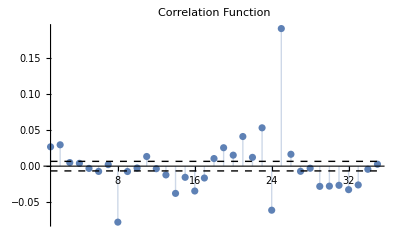

```mathematica
traditionalModelHourly["ACFPlot"]
```

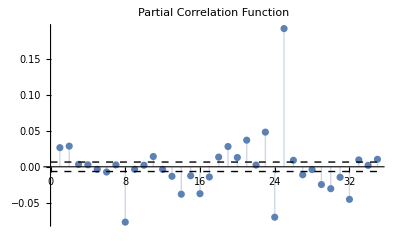

```mathematica
traditionalModelHourly["PACFPlot"]
```

```mathematica
AutocorrelationTest[traditionalModelHourly["FitResiduals"]]
```

1.12932×10^-141

### 2.3 Plot results

#### 2.3.1 For monthly data

Initialisation of the SARIMA model

```mathematica
traditionalModelMonthly["CandidateModels"][[1]]
```

SARIMAProcess[-373637.,{0.382017},0,{},{12,{},1,{-0.839147,0.243915}},2.30377×10^12]

```mathematica
traditionalModelMonthlyInit=SARIMAProcess[-373636.6505401716,{0.3820168859833999},0,{},{12,{},1,{-0.8391471168203113,0.24391517497281967}},2.303767125441893*^12,trainingMonthly]
```

SARIMAProcess[-373637.,{0.382017},0,{},{12,{},1,{-0.839147,0.243915}},2.30377×10^12,TimeSeries[…]]

Predictions for the test data.

```mathematica
ticksM=monthlyTotalDemandTS["Times"][[Range[6,180,24]]]
```

{3452803200,3515875200,3579033600,3642105600,3705264000,3768336000,3831494400,3894566400}

```mathematica
yearsM={"2009","2011","2013","2015","2027","2019","2021","2023"}
```

{2009,2011,2013,2015,2027,2019,2021,2023}

SARIMA model fit to UK electricity demand data between 2019 and 2021

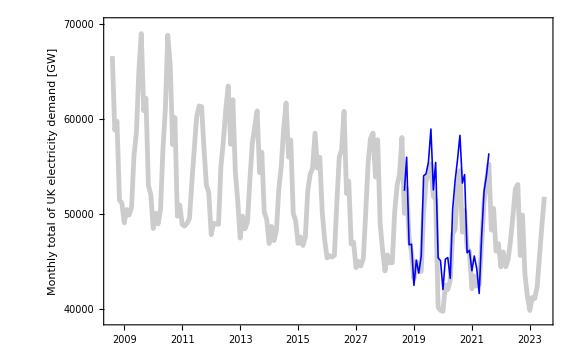

```mathematica
figC3=ListLinePlot[{monthlyTotalDemandTS/1000,
RandomFunction[traditionalModelMonthlyInit,{1,36}]/1000},

PlotRangeClipping->False,
PlotRange->{monthlyTotalDemandTS["Times"][[{1,-1}]],{39000,70000}},
PlotStyle->{
Directive[RGBColor[0.5,0.5,0.5,0.4],Thickness[0.006]],
Directive[Blue,Thickness[0.002]]},

Frame->{True,True,False, False},
FrameLabel->{None, "Monthly total of UK electricity demand [GW]"},
FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{ticksM,yearsM}]],
	            Range[40000,70000,10000]},
	FrameTicksStyle->{12, 12},
ImageSize->Large]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","FigureC3.png"}],figC3];
```

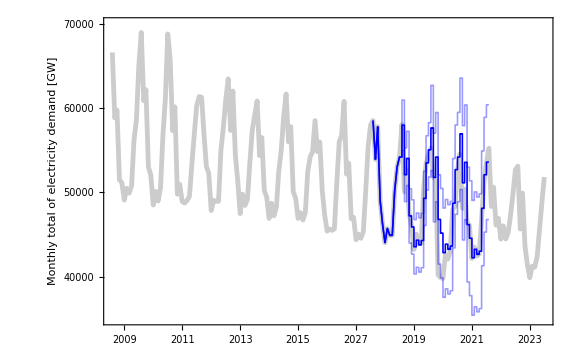

```mathematica
Show[
ListLinePlot[monthlyTotalDemandTS/1000,

PlotStyle->{
Directive[RGBColor[0.5,0.5,0.5,0.4],Thickness[0.006]],
Directive[RGBColor[0.5,0.5,0.5,0.4],Thickness[0.006]]},
PlotRangeClipping->False,
PlotRange->{monthlyTotalDemandTS["Times"][[{1,-1}]],{35000,70000}},

Frame->{True,True,False, False},
FrameLabel->{None, "Monthly total of electricity demand [GW]"},
FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{ticksM,yearsM}]],
	            Range[40000,70000,10000]},
	FrameTicksStyle->{12, 12}],

Plot[{traditionalModelMonthly[t]/1000,traditionalModelMonthly["PredictionLimits"][t]/1000},{t,3723753600,3849984000},
PlotStyle->{Directive[Blue,Thickness[0.002]],Directive[RGBColor[0,0,1,0.4],Thickness[0.002]]}],
ImageSize->Large
]
```

```mathematica
predictionsMonthly=RandomFunction[traditionalModelMonthlyInit,{1,36}]
```

TemporalData[…]

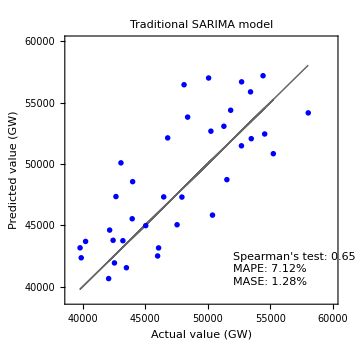

```mathematica
figC4=ListPlot[{{(testingMonthly["Values"])[[#]]/1000,(testingMonthly["Values"])[[#]]/1000}&/@Range[36],
{(testingMonthly["Values"])[[#]]/1000,(RandomFunction[traditionalModelMonthlyInit,{1,36}]["Values"])[[#]]/1000}&/@Range[36]},
Joined->{True,False},
PlotStyle->{
Directive[GrayLevel[0.4],Thickness[0.003]],
Directive[Blue,Thickness[0.002]]},

PlotLabel->Style["Traditional SARIMA model",Bold,FontSize->14],
AspectRatio->1,
PlotRange->{{39000,60000},{39000,60000}},
PlotRangeClipping->False,

Frame->{True,True,False, False},
FrameLabel->{"Actual value (GW)", "Predicted value (GW)"},
FrameTicks->{Range[40000,60000,5000],
	            Range[40000,60000,5000]},
	FrameTicksStyle->{12, 12},
ImageSize->Medium,

Epilog->{
Style[Text[Row[{"Spearman's test: ",ResourceFunction["DecimalRound"][SpearmanRankTest[testingMonthly["Values"],RandomFunction[traditionalModelMonthlyInit,{1,36}]["Values"],"TestStatistic"],2]}], {52000,42000},{-1,-1}], 
                       FontColor->GrayLevel[0.4], FontSize->12],
Style[Text[Row[{"MAPE: ",
ResourceFunction["DecimalRound"][mape[RandomFunction[traditionalModelMonthlyInit,{1,36}]["Values"],testingMonthly["Values"]],3],"%"}], {52000,41000},{-1,-1}], 
                       FontColor->GrayLevel[0.4], FontSize->12],
Style[Text[Row[{"MASE: ",
ResourceFunction["DecimalRound"][mase[RandomFunction[traditionalModelMonthlyInit,{1,36}]["Values"],testingMonthly["Values"]],3],"%"}], {52000,40000},{-1,-1}], 
                       FontColor->GrayLevel[0.4], FontSize->12]
}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","FigureC4.png"}],figC4];
```

Mean MAPE error over 5000 realisation of the SARIMA model.

For 2019 monthly data.

```mathematica
Mean[Table[mape[RandomFunction[traditionalModelMonthlyInit,{1,12}]["Values"],testingMonthly["Values"][[;;12]]],5000]]
```

6.30254

For 2019 to 2021 monthly data.

```mathematica
Mean[Table[mape[RandomFunction[traditionalModelMonthlyInit,{1,36}]["Values"],testingMonthly["Values"]],5000]]
```

7.11388

#### 2.3.2 For hourly data

Initialisation of the SARMA model

```mathematica
traditionalModelHourly["CandidateModels"][[1]]
```

SARMAProcess[826.012,{1.57815,-0.858788,0.236937},{},{12,{0.0170132,0.817276,-0.0501449},{}},1.81598×10^6]

```mathematica
traditionalModelHourlyInit=SARMAProcess[826.0122272153183,{1.578148998699887,-0.8587879852103035,0.23693747935234663},{},{12,{0.017013172497278243,0.8172761190006227,-0.05014488721971833},{}},1.8159830599526705*^6,trainingHourly]
```

SARMAProcess[826.012,{1.57815,-0.858788,0.236937},{},{12,{0.0170132,0.817276,-0.0501449},{}},1.81598×10^6,TemporalData[TimeSeries, «1»]]

```mathematica
yearsH={2010,2012,2014,2016,2018,2020,2022}
```

{2010,2012,2014,2016,2018,2020,2022}

```mathematica
ticksH=hourlyDemandTS["Times"][[Range[13104,131472,17472]]]
```

{3486927600,3549826800,3612726000,3675625200,3738524400,3801423600,3864322800}

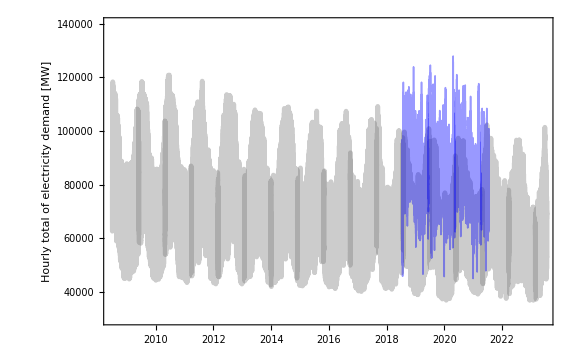

```mathematica
figC5=ListLinePlot[{hourlyDemandTS,
RandomFunction[traditionalModelHourlyInit,{1,26304}]},

PlotRangeClipping->False,
PlotRange->{monthlyTotalDemandTS["Times"][[{1,-1}]],{30000,140000}},
PlotStyle->{
Directive[RGBColor[0.5,0.5,0.5,0.4],Thickness[0.006]],
Directive[RGBColor[0,0,1,0.4],Thickness[0.002]]},

Frame->{True,True,False, False},
FrameLabel->{None, "Hourly total of electricity demand [MW]"},
FrameTicks->{Map[{#⟦1⟧,#⟦2⟧,0}&, Transpose[{ticksH,yearsH}]],
	            Range[40000,140000,20000]},
	FrameTicksStyle->{12, 12},
ImageSize->Large]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","FigureC5.png"}],figC5];
```

For 2019 to 2021 hourly data.

```mathematica
Mean[Table[mape[RandomFunction[traditionalModelHourlyInit,{1,29304}]["Values"],testingHourly["Values"]],1000]]
```

42.5719